```mathematica
Monitor[Table[Length[ShowForNodesFull[k,Last][[1]]],{k,5,10}],k]
```

{5,25,115,505,2155,9025}

```mathematica
{5,25,115,505,2155,9025}/5
```

{1,5,23,101,431,1805}

```mathematica
LinearRecurrence[{4,9,-36},{1,5,23},30] (*Harvey P.Dale,Nov 30 2011*)
```

{1,5,23,101,431,1805,7463,30581,124511,504605,2038103,8211461,33022991,132623405,532087943,2133134741,8546887871,34230598205,137051532983,548593552421,2195536471151,8785632669005,35152991029223,140643345176501,562667523884831,2250952525075805,9004657388912663,36021171421478981,144092311283400911,576392121926058605}

```mathematica
LinearRecurrence[{7,-12},{1,5},30]==LinearRecurrence[{4,9,-36},{1,5,23},30]
```

True

```mathematica
LinearRecurrence[{a,b},{1,5},10]
```

{1,5,5 a+b,5 b+a (5 a+b),5 a^3+10 a b+a^2 b+b^2,5 a^4+15 a^2 b+a^3 b+5 b^2+2 a b^2,5 a^5+20 a^3 b+a^4 b+15 a b^2+3 a^2 b^2+b^3,5 a^6+25 a^4 b+a^5 b+30 a^2 b^2+4 a^3 b^2+5 b^3+3 a b^3,5 a^7+30 a^5 b+a^6 b+50 a^3 b^2+5 a^4 b^2+20 a b^3+6 a^2 b^3+b^4,5 a^8+35 a^6 b+a^7 b+75 a^4 b^2+6 a^5 b^2+50 a^2 b^3+10 a^3 b^3+5 b^4+4 a b^4}

```mathematica
Monitor[Table[Length[ShowForNodesFull[k,First][[1]]],{k,5,11}],k]
```

{5,11,16,8,13,13,17}

```mathematica
Clear[ShowForNodesFullChrom];ShowForNodesFullChrom[nodes_,operation_:First]:=Block[
{
part1=operation[QuadrilateralsWithPattern[nodes,1]],
part2=operation[QuadrilateralsWithPattern[nodes,2]],
part3=operation[QuadrilateralsWithPattern[nodes,3]],
part4=operation[QuadrilateralsWithPattern[nodes,4]],
part5=operation[QuadrilateralsWithPattern[nodes,5]]
},
Block[
{
e1=EdgeList[GraphComplement[GraphFromSets[part1]]],
e2=EdgeList[GraphComplement[GraphFromSets[part2]]],
e3=EdgeList[GraphComplement[GraphFromSets[part3]]],
e4=EdgeList[GraphComplement[GraphFromSets[part4]]],
e5=EdgeList[GraphComplement[GraphFromSets[part5]]]
},
ChromaticPolynomial[EdgeDelete[CompleteGraph[nodes],DeleteDuplicates[Join[e1,e2,e3,e4,e5]]],x]
]
]
```

```mathematica
Clear[ShowForNodesFullGraph];ShowForNodesFullGraph[nodes_,operation_:First]:=Block[
{
part1=operation[QuadrilateralsWithPattern[nodes,1]],
part2=operation[QuadrilateralsWithPattern[nodes,2]],
part3=operation[QuadrilateralsWithPattern[nodes,3]],
part4=operation[QuadrilateralsWithPattern[nodes,4]],
part5=operation[QuadrilateralsWithPattern[nodes,5]]
},
Block[
{
e1=EdgeList[GraphComplement[GraphFromSets[part1]]],
e2=EdgeList[GraphComplement[GraphFromSets[part2]]],
e3=EdgeList[GraphComplement[GraphFromSets[part3]]],
e4=EdgeList[GraphComplement[GraphFromSets[part4]]],
e5=EdgeList[GraphComplement[GraphFromSets[part5]]]
},
EdgeDelete[CompleteGraph[nodes],DeleteDuplicates[Join[e1,e2,e3,e4,e5]]]
]
]
```

```mathematica
Monitor[Table[Solve[ShowForNodesFullChrom[k,Last]==0,x],{k,5,12}],k]//TableForm
```

x→0 | x→1 | x→1-ⅈ | x→1+ⅈ | x→2 |  |  |  |  |  |  | 
x→0 | x→0 | x→1 | x→1-ⅈ | x→1+ⅈ | x→2 |  |  |  |  |  | 
x→0 | x→0 | x→0 | x→1 | x→1-ⅈ | x→1+ⅈ | x→2 |  |  |  |  | 
x→0 | x→0 | x→0 | x→0 | x→1 | x→1-ⅈ | x→1+ⅈ | x→2 |  |  |  | 
x→0 | x→0 | x→0 | x→0 | x→0 | x→1 | x→1-ⅈ | x→1+ⅈ | x→2 |  |  | 
x→0 | x→0 | x→0 | x→0 | x→0 | x→0 | x→1 | x→1-ⅈ | x→1+ⅈ | x→2 |  | 
x→0 | x→0 | x→0 | x→0 | x→0 | x→0 | x→0 | x→1 | x→1-ⅈ | x→1+ⅈ | x→2 | 
x→0 | x→0 | x→0 | x→0 | x→0 | x→0 | x→0 | x→0 | x→1 | x→1-ⅈ | x→1+ⅈ | x→2

```mathematica
Monitor[Table[3*k-6-EdgeCount[ShowForNodesFullGraph[k,First]],{k,5,14}],k]
```

{4,4,4,2,1,-2,-4,-9,-14,-20}

```mathematica
Differences[{4,4,4,2,1,-2,-4,-9,-14,-20}]
```

{0,0,-2,-1,-3,-2,-5,-5,-6}

```mathematica
Monitor[Table[3*k-6-EdgeCount[ShowForNodesFullGraph[k,Last]],{k,5,14}],k]
```

{4,7,10,13,16,19,22,25,28,31}

```mathematica
Differences[{4,7,10,13,16,19,22,25,28,31}]
```

{3,3,3,3,3,3,3,3,3}

```mathematica
3*13-6
```

33

```mathematica
EdgeCount[ShowForNodesFullGraph[13,Last]]
```

5

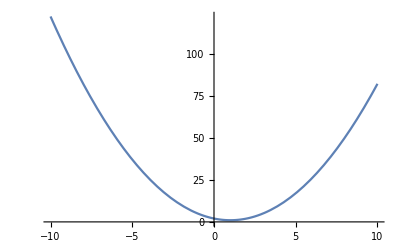

```mathematica
Plot[2-2 x+x^2,{x,-10,10}]
```